## Controllability for a discrete system (Problem 5.14)

If a continuous system is controllable, what about its discretization?

```mathematica
Clear["Global`*"];
```

```mathematica
G0 = TransferFunctionModel[1/(1+s^2),s];
Sys0 = StateSpaceModel[G0]
```

010-101100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Wc0 = ControllabilityMatrix[Sys0];  {TraditionalForm[Wc0],MatrixRank[Wc0]}
```

{(0 | 1
1 | 0),2}

```mathematica
SysD0=ToDiscreteTimeModel[Sys0,Ts,z,Method -> "ZeroOrderHold"]
```

Cos[Ts]Sin[Ts]1-Cos[Ts]-Sin[Ts]Cos[Ts]Sin[Ts]100TsStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
WcD0 = ControllabilityMatrix[SysD0]// FullSimplify;  {TraditionalForm[WcD0],MatrixRank[WcD0]}
```

{(1-cos(Ts) | cos(Ts)-cos(2 Ts)
sin(Ts) | sin(Ts) (2 cos(Ts)-1)),2}

```mathematica
det=Det[WcD0] // Factor // Simplify
```

2 (-1+Cos[Ts]) Sin[Ts]

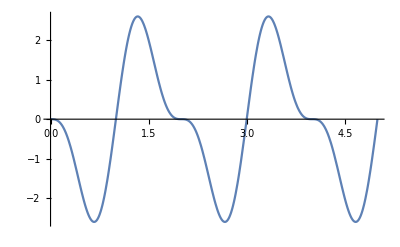

```mathematica
Plot[Det[WcD0]/.Ts->m π,{m,0,5}]
```

We see that controllability fails for Ts=π , 2π, ....  with the even set being cubic zeros
and the odd  set being ordinary (linear) zeros

```mathematica
{SysD0/.Ts->π,SysD0/.Ts->2π}
```

{-1020-10100πStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,1000101002 πStateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic}

The mathematical issue is that the input coupling vanishes.  Why does this happen?  
Why are the even and odd cases different?

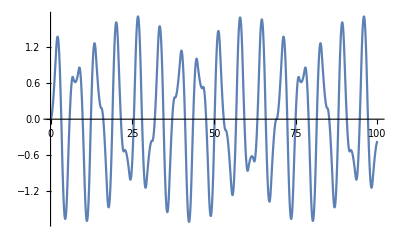

```mathematica
tmax=100;
y0=OutputResponse[Sys0,SquareWave[t/(1.1π)],{t,0,tmax}];
Plot[y0,{t,0,tmax}]
```

```mathematica
Series[det,{Ts,π,3}]
```

4 (Ts-π)-5/3 (Ts-π)^3+O[Ts-π]^4

```mathematica
Series[det,{Ts,2π,5}]
```

-(Ts-2 π)^3+1/4 (Ts-2 π)^5+O[Ts-2 π]^6